```mathematica
Clear[DPlot];
DPlot[eqn_,u_,x_,fic_,sic_,dom_,codom_:{},n_:10,epilogValues_:{},styles_:{}]:=Module[{i,j,k,eqs,fics,sics,aics,temp,temp2,ics,plots,f,f1,f2,fArg,fArg1,fArg2},
(*initialise local variables that need initialising*)
eqs={};
fics={};
sics={};
temp={};
temp2={};
ics={};
plots={};

(*generate first order inital condition e.g. y[x]==a*)
If[Length[fic]!=0,
(*function generates a range of initial conditions based on a range of values*)
(*{y[x],a,b} maps to {y[x]==a+0*(b-a)/n,y[x]==a+1*(b-a)/n...y[x]==a+n*(b-a)/n}*)
f=fArg|->(fArg[[1]]==#)&/@Subdivide[fArg[[2]],fArg[[3]],n];
If[TrueQ[fic[[1,0]]==List],
fics=f[#]&/@fic;
,(*else*)
fics={f[fic]};
];
];

(*generate second order initial conditions e.g. y'[x]==a*)
If[Length[sic]!=0,
(*function generates a range of initial conditions based on a range of values*)
(*{y[x],a,b} maps to {y[x]==a+0*(b-a)/n,y[x]==a+1*(b-a)/n...y[x]==a+n*(b-a)/n}*)
f=fArg|->(fArg[[1]]==#)&/@Subdivide[fArg[[2]],fArg[[3]],n];
If[TrueQ[sic[[1,0]]==List],
sics=f[#]&/@sic;
,(*else*)
sics={f[sic]};
];
];

(*combine the first and second order initial conditions. When all is said and done, all initial conditions are created equal, however some are created more equal than others, hense first order initial conditions are put in the list first*)
aics=Join[fics,sics];
(*if there is only one initial condition being varied then no extra processing is needed*)
(*if more than one initial condition is being varied then all combinations of varied initial conditions much be taken, akin to sampling a grid of points on all sides of a n-cube*) 
If[Length[aics]!=1,
While[Length[aics]>=2,
temp={};
For[i=0,i<Length[aics[[-2]]],i++,
If[TrueQ[aics[[-1,1,0]]==List],
For[j=0,j<Length[aics[[-1]]],j++,
AppendTo[temp,Append[aics[[-1,j+1]],aics[[-2,i+1]]]];
];
,(*else*)
For[j=0,j<Length[aics[[-1]]],j++,
AppendTo[temp,{aics[[-1,j+1]],aics[[-2,i+1]]}];
];
];
];
aics=Take[aics,Length[aics]-2];
AppendTo[aics,temp];
temp={};
];
ics=aics[[1]];
,(*else*)
ics={#}&/@aics[[1]];
];

(*DSolve*)
For[i=0,i<Length[ics],i++,
AppendTo[eqs,DSolve[{eqn,ics[[i+1]]},u,x][[All,1,2]]];
];

(*Plot*)
For[i=0,i<Length[eqs],i++,
If[TrueQ[codom=={}],
AppendTo[plots,Plot[eqs[[i+1,1]],{x,dom[[1]],dom[[2]]},Epilog->epilogValues,PlotStyle->styles]];
,(*else*)
AppendTo[plots,Plot[eqs[[i+1,1]],{x,dom[[1]],dom[[2]]},PlotRange->codom,Epilog->epilogValues,PlotStyle->styles]];
];
];
Return[Show[plots]];
]
```

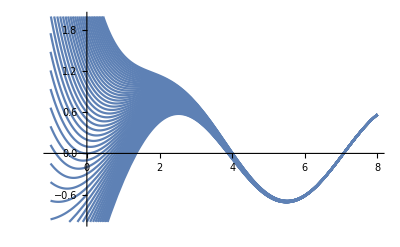

```mathematica
DPlot[y'[x]+y[x]==Sin[x],y[x],x,{y[0],-2,3},{},{-1,8},{-1,2},50]
```

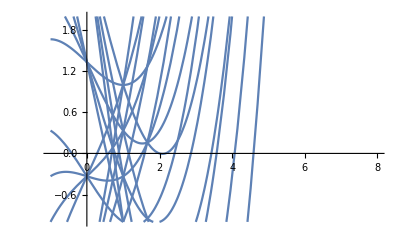

```mathematica
DPlot[y''[x]==x,y[x],x,{{y[0],-2,3},{y[1],-1,1}},{},{-1,8},{-1,2},3]
```

```mathematica
Clear[DStreamPlot];
DStreamPlot[eqn_,u_,x_,dom_,codom_:{},res_:7]:=Module[{i,j,plots,xVals,localX,ics,epilogPoints,temp},
(*initialise local variables*)
plots={};
ics={};
xVals=Subdivide[dom[[1]],dom[[2]],res];
epilogPoints={};

(*Create epilog data for points*)
For[i=0,i<Length[xVals],i++,
AppendTo[epilogPoints,ColorData[97,"ColorList"][[Mod[i,15]+1]]];
temp=Subdivide[codom[[1]],codom[[2]],res];
For[j=0,j<res+1,j++,
AppendTo[epilogPoints,Point[{xVals[[i+1]],temp[[j+1]]}]];
];
];

(*Generate a DPlot for each color desired*)
For[i=0,i<Length[xVals],i++,
AppendTo[ics,{u/.x->xVals[[i+1]],codom[[1]],codom[[2]]}];
];
For[i=0,i<Length[ics],i++,
AppendTo[plots,DPlot[eqn,u,x,ics[[i+1]],{},dom,codom,res,{PointSize[Large],epilogPoints},{ColorData[97,"ColorList"][[Mod[i,15]+1]]}]];
];
Return[Show[plots]];
];
```

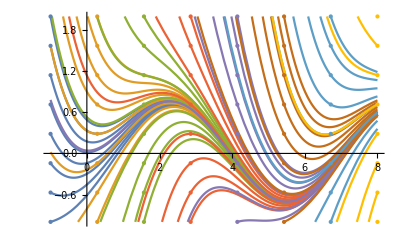

```mathematica
DStreamPlot[y'[x]+y[x]==Sin[x],y[x],x,{-1,8},{-1,2},7]
```